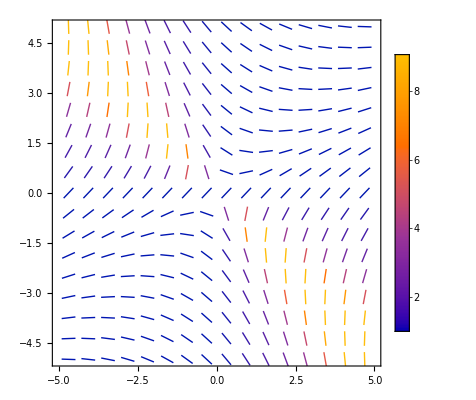

```mathematica
dfield = VectorPlot[{1, (x-y)/(x+y)},{x, -5, 5}, {y, -5, 5}, PlotLegends->Automatic, VectorPoints->"Regular",VectorMarkers->"Segment", VectorSizes->Small, VectorStyle->Thick]
```

```mathematica
desol=DSolve[y'[x]==(x-y[x])/(x+y[x]),y[x],x]
```

{{y[x]→-x-√(ⅇ^(2 C[1])+2 x^2)},{y[x]→-x+√(ⅇ^(2 C[1])+2 x^2)}}

```mathematica
sol1={y[x]->-x+√(ⅇ^(2 C[1])+2 x^2)};
```

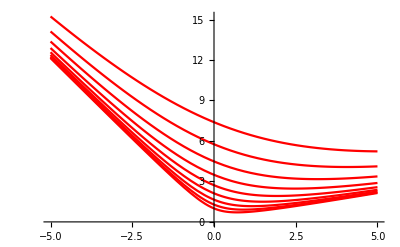

```mathematica
sols=Plot[Evaluate[y[x]/.sol1/.Table[{{C[1]->a}},{a, 0,2, 0.25}]], {x, -5,5}, PlotStyle->Red]
```

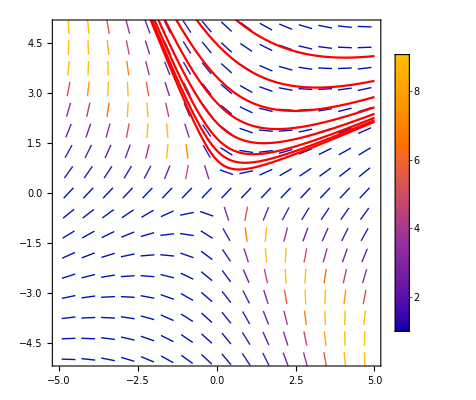

```mathematica
deandsols =Show[dfield,sols]
```

```mathematica
Export["de-dfield-with-sols.pdf", deandsols]
```

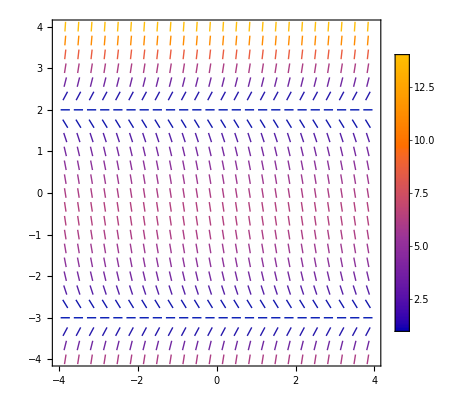

```mathematica
autdfield = VectorPlot[{1, y^2+y-6},{x, -4, 4}, {y, -4, 4}, PlotLegends->Automatic, VectorMarkers->"Segment",VectorPoints->{"Regular",24}, VectorSizes->Small]
```

```mathematica
SetDirectory["D:\\Users\\Matt\\OneDrive\\Mathematics\\calculus-notes\\Figures"]
```

D:\Users\Matt\OneDrive\Mathematics\calculus-notes\Figures

```mathematica
Export["de-aut-dfield.pdf", autdfield];
```

```mathematica
f[x_]:=Piecewise[{{0, 0<=x<2}, {4, x >= 2}}];
```

```mathematica
sol =DSolve[{y'[x]==-3y[x]+f[x], y[0]==2},y[x],x]
```

{{y[x]→Piecewise[{{2 ⅇ^(-3 x), x≤2}, {2/3 ⅇ^(-3 x) (3-2 ⅇ^6+2 ⅇ^(3 x)), True}}]}}

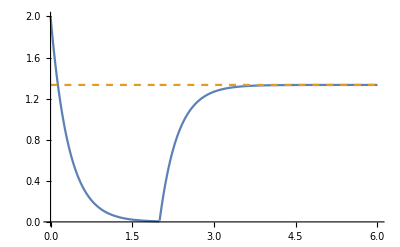

```mathematica
Plot[Evaluate[{y[x]/. sol, 4/3}], {x, 0, 6}, PlotRange->{Automatic, {0,2}}, PlotStyle->{Automatic, Dashed}]
```

```mathematica
sol1=DSolve[{y''[t]+2y'[t]+5y[t]==0, y[0]==3, y'[0]==2},y[t],t]
```

{{y[t]→1/2 ⅇ^-t (6 Cos[2 t]+5 Sin[2 t])}}

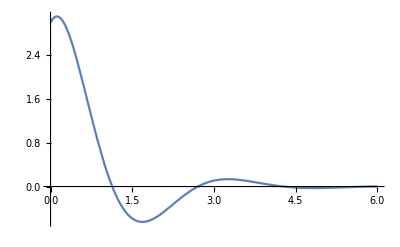

```mathematica
Plot[y[t]/.sol1, {t, 0, 6}, PlotRange->Full]
```

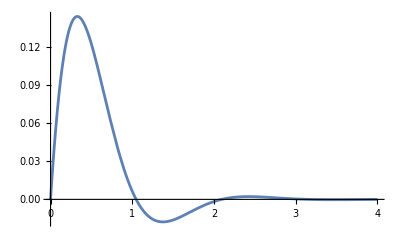

```mathematica
f[t_]:=1/3*Exp[-2t]Sin[3t];
Plot[f[t], {t,0, 4}]
```

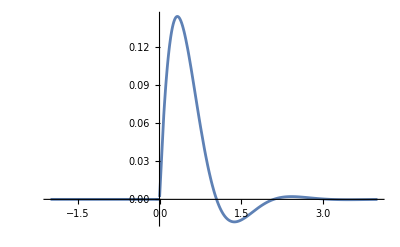

```mathematica
Plot[Piecewise[{{0, t<0},{f[t],t>0}}], {t, -2, 4},PlotRange->All]
```

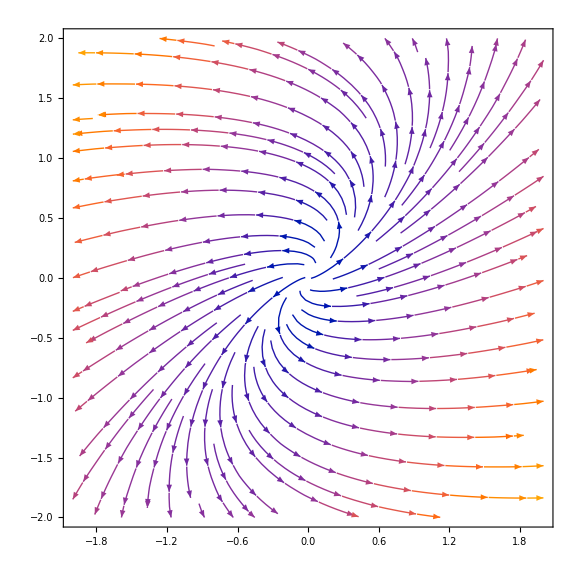

```mathematica
A=({{3, -2}, {1, 1}});
vf = A.{x,y};
Show[
StreamPlot[vf, {x, -2, 2}, {y, -2, 2}],
ParametricPlot[Eigenvectors[A]*t, {t, -10, 10}, PlotStyle->Red]
, ImageSize->Large]
```

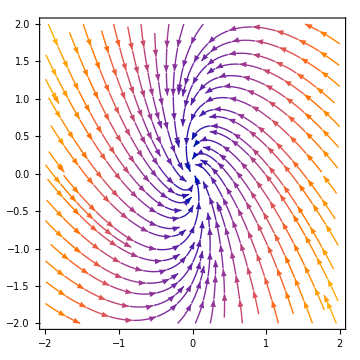

```mathematica
A=({{-4, -1}, {5, -2}});
vf = A.{x,y};
Show[
StreamPlot[vf, {x, -2, 2}, {y, -2, 2}],
ParametricPlot[Eigenvectors[A]*t, {t, -10, 10}, PlotStyle->Red]
, ImageSize->Large]
```

```mathematica
A - IdentityMatrix[2](-3+2I)//RowReduce//MatrixForm
```

(1 | 1/5-(2 ⅈ)/5
0 | 0)